```mathematica
eq=D[u[x,t], t]+β D[(u[x,t]^2), x]+d D[u[x,t], x,x,x]
```

u^(0,1)[x,t]+2 β u[x,t] u^(1,0)[x,t]+d u^(3,0)[x,t]

```mathematica
u[x_,t_]=A Cosh[(x-v t)/l]^-2;
```

```mathematica
eq//Simplify
```

(2 A Sech[(-t v+x)/l]^2 Tanh[(-t v+x)/l] (l^2 v+(8 d-2 A l^2 β) Sech[(-t v+x)/l]^2-4 d Tanh[(-t v+x)/l]^2))/l^3

```mathematica
Tanh[x]^2==1-Sech[x]^2//Simplify
```

True

```mathematica
l^2 v+(8 d-2 A l^2 β) Sech[(-t v+x)/l]^2-4 d Tanh[(-t v+x)/l]^2/.{Tanh[x__]^2->1-Sech[x]^2}//Simplify
```

-4 d+l^2 v+2 (6 d-A l^2 β) Sech[(-t v+x)/l]^2

```mathematica
v=Solve[-4 d+l^2 v==0,v]⟦1,1,2⟧
```

(4 d)/l^2

```mathematica
ClearAll[l]
l=Solve[6 d-A l^2 β==0,l]⟦2,1,2⟧
```

(√6 √d)/(√A √β)

```mathematica
v
```

(2 A β)/3

```mathematica
l=Sqrt[6d/A/β]
```

√6 √(d/(A β))

```mathematica
d=2;
A=-0.01;
```

```mathematica
Clear[A]
```

```mathematica
Manipulate[Plot[A Sech[(√β (x))/(√(-6A))]^2,{x,-1,1},PlotRange->All],{β,1000,0}]
```

-100

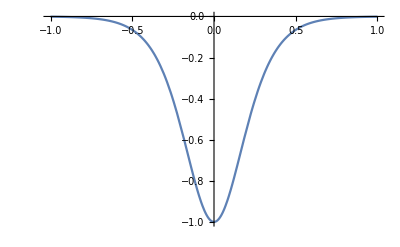

```mathematica
β=-100
Plot[u[x,0],{x,-1,1}]
```